```mathematica
<<FeynArts`
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
loop
```

loop

> Top. 1 afbf/cgdgeg/fg.m, 0 diagrams

> Top. 2 afbg/cfdgeg/fg.m, 0 diagrams

> Top. 3 afbg/cgdfeg/fg.m, 0 diagrams

> Top. 4 afbg/cgdgef/fg.m, 0 diagrams

> Top. 5 afbg/cgdfef/gf.m, 0 diagrams

> Top. 6 afbg/cfdgef/gf.m, 0 diagrams

> Top. 7 afbg/cfdfeg/gf.m, 0 diagrams

> Top. 8 afbf/cgdgef/gf.m, 0 diagrams

> Top. 9 afbf/cgdfeg/gf.m, 0 diagrams

> Top. 10 afbf/cfdgeg/gf.m, 0 diagrams

> Top. 11 afbf/cgdgeh/fhgh.m, 0 diagrams

> Top. 12 afbf/cgdheg/fhgh.m, 0 diagrams

> Top. 13 afbf/cgdheh/fggh.m, 0 diagrams

> Top. 14 afbg/cfdgeh/fhgh.m, 0 diagrams

> Top. 15 afbg/cfdheg/fhgh.m, 0 diagrams

> Top. 16 afbg/cfdheh/fggh.m, 0 diagrams

> Top. 17 afbg/cgdfeh/fhgh.m, 0 diagrams

> Top. 18 afbg/cgdhef/fhgh.m, 0 diagrams

> Top. 19 afbg/cgdheh/fgfh.m, 0 diagrams

> Top. 20 afbg/chdfeg/fhgh.m, 0 diagrams

> Top. 21 afbg/chdfeh/fggh.m, 0 diagrams

> Top. 22 afbg/chdgef/fhgh.m, 0 diagrams

> Top. 23 afbg/chdgeh/fgfh.m, 0 diagrams

> Top. 24 afbg/chdhef/fggh.m, 0 diagrams

> Top. 25 afbg/chdheg/fgfh.m, 0 diagrams

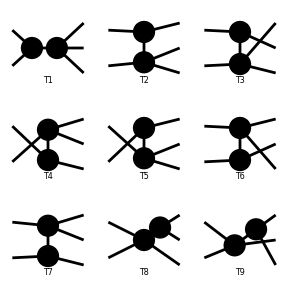

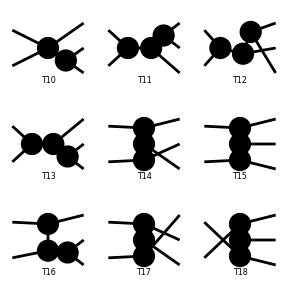

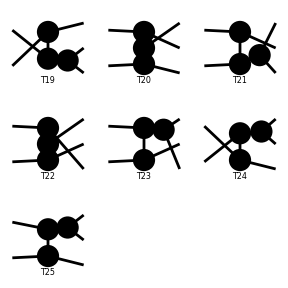

FeynArtsGraphics[2→3][([T1] | [T2] | [T3]
[T4] | [T5] | [T6]
[T7] | [T8] | [T9]),([T10] | [T11] | [T12]
[T13] | [T14] | [T15]
[T16] | [T17] | [T18]),([T19] | [T20] | [T21]
[T22] | [T23] | [T24]
[T25] | Null | Null)]

```mathematica
top=CreateTopologies[0,2->3,ExcludeTopologies->Tadpoles];
Paint[top]
```

```mathematica
top;
```

```mathematica
ins1=InsertFields[top,{S[1],S[1]}->{S[1],S[1],S[1]},Model->SM,InsertionLevel->{Classes},ExcludeParticles->{V,F},ExcludeFieldPoints->{FieldPoint[0][S,S,S,S]}];
```

loading generic model file /Users/zeno/Documents/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /Users/zeno/Documents/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

Excluding 2 Generic, 12 Classes, and 28 Particles fields

Excluding 6 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Classes}

> Top. 1: 0 Classes insertions

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 0 Classes insertions

> Top. 9: 0 Classes insertions

> Top. 10: 0 Classes insertions

> Top. 11: 1 Classes insertion

> Top. 12: 1 Classes insertion

> Top. 13: 1 Classes insertion

> Top. 14: 1 Classes insertion

> Top. 15: 1 Classes insertion

> Top. 16: 1 Classes insertion

> Top. 17: 1 Classes insertion

> Top. 18: 1 Classes insertion

> Top. 19: 1 Classes insertion

> Top. 20: 1 Classes insertion

> Top. 21: 1 Classes insertion

> Top. 22: 1 Classes insertion

> Top. 23: 1 Classes insertion

> Top. 24: 1 Classes insertion

> Top. 25: 1 Classes insertion

Restoring 2 Generic, 12 Classes, and 28 Particles fields

Restoring 6 field point(s)

in total: 15 Classes insertions

> Top. 1 afbf/cgdgeh/fhgh.m, 0 diagrams

> Top. 2 afbf/cgdheg/fhgh.m, 0 diagrams

> Top. 3 afbf/cgdheh/fggh.m, 0 diagrams

> Top. 4 afbg/cfdgeh/fhgh.m, 0 diagrams

> Top. 5 afbg/cfdheg/fhgh.m, 0 diagrams

> Top. 6 afbg/cfdheh/fggh.m, 0 diagrams

> Top. 7 afbg/cgdfeh/fhgh.m, 0 diagrams

> Top. 8 afbg/cgdhef/fhgh.m, 0 diagrams

> Top. 9 afbg/cgdheh/fgfh.m, 0 diagrams

> Top. 10 afbg/chdfeg/fhgh.m, 0 diagrams

> Top. 11 afbg/chdfeh/fggh.m, 0 diagrams

> Top. 12 afbg/chdgef/fhgh.m, 0 diagrams

> Top. 13 afbg/chdgeh/fgfh.m, 0 diagrams

> Top. 14 afbg/chdhef/fggh.m, 0 diagrams

> Top. 15 afbg/chdheg/fgfh.m, 0 diagrams

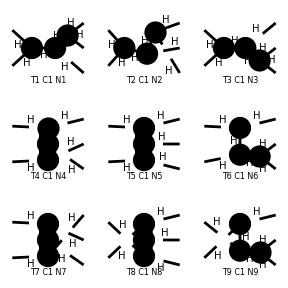

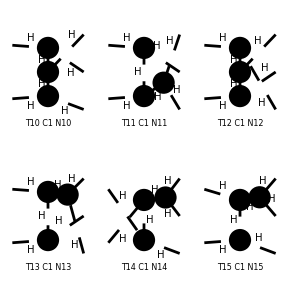

FeynArtsGraphics[{H,H}→{H,H,H}][([T1 C1 N1] | [T2 C1 N2] | [T3 C1 N3]
[T4 C1 N4] | [T5 C1 N5] | [T6 C1 N6]
[T7 C1 N7] | [T8 C1 N8] | [T9 C1 N9]),([T10 C1 N10] | [T11 C1 N11] | [T12 C1 N12]
[T13 C1 N13] | [T14 C1 N14] | [T15 C1 N15]
Null | Null | Null)]

```mathematica
Paint[ins1]
```

```mathematica
amp=CreateFeynAmp[ins1];
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

> Top. 5: 1 Classes amplitude

> Top. 6: 1 Classes amplitude

> Top. 7: 1 Classes amplitude

> Top. 8: 1 Classes amplitude

> Top. 9: 1 Classes amplitude

> Top. 10: 1 Classes amplitude

> Top. 11: 1 Classes amplitude

> Top. 12: 1 Classes amplitude

> Top. 13: 1 Classes amplitude

> Top. 14: 1 Classes amplitude

> Top. 15: 1 Classes amplitude

in total: 15 Classes amplitudes

```mathematica
FullForm[Sum[amp[[i]][[3]],{i,1,Length[amp]}]];
```

```mathematica
SP[v_,m_]:=v[[1]]^2-v[[2]]^2-v[[3]]^2-v[[4]]^2-m^2
```

```mathematica
k={{1,2,3,4},{0,2,1,0},{1,1,0,0}}
p={{1,2,0,4},{1,2,1,1}}
```

{{1,2,3,4},{0,2,1,0},{1,1,0,0}}

{{1,2,0,4},{1,2,1,1}}

```mathematica
Sum[amp[[i]][[3]],{i,1,Length[amp]}];
```

```mathematica
ClearAll[k,p,SP]
```

```mathematica
(*amp5p[p1_,p2_,k1_,k2_,k3_]:=*)

Simplify[8 MW^3SW^3/(27 EL^3 MH^6)Sum[amp[[i]][[3]],{i,1,Length[amp]}]//.{PropagatorDenominator:>SP,FourMomentum[Incoming,x_]->p[x],FourMomentum[Outgoing,x_]->k[x]}(*//.{(x_)^2:>SP[x]}*)]/.{MH->0}/.{k[1]->k1,k[2]->k2,k[3]->k3,p[1]->p1,p[2]->p2}
```

-SP[-k1-k2,0] SP[k1+k2+k3,0]-SP[-k1-k3,0] SP[k1+k2+k3,0]-SP[k2+k3,0] SP[k1+k2+k3,0]-SP[k2+k3,0] SP[k1-p2,0]-SP[k1+k3,0] SP[k2-p2,0]-SP[k1+k2,0] SP[k1+k2-p2,0]-SP[k1+k2,0] SP[k3-p2,0]-SP[k1+k3,0] SP[k1+k3-p2,0]-SP[k2+k3,0] SP[k2+k3-p2,0]-SP[k1+k2-p2,0] SP[-k1+p2,0]-SP[k1+k3-p2,0] SP[-k1+p2,0]-SP[k1+k2-p2,0] SP[-k2+p2,0]-SP[k2+k3-p2,0] SP[-k2+p2,0]-SP[k1+k3-p2,0] SP[-k3+p2,0]-SP[k2+k3-p2,0] SP[-k3+p2,0]

```mathematica
amp5p[p1_,p2_,k1_,k2_,k3_]:=-SP[-k1-k2,0] SP[k1+k2+k3,0]-SP[-k1-k3,0] SP[k1+k2+k3,0]-SP[k2+k3,0] SP[k1+k2+k3,0]-SP[k2+k3,0] SP[k1-p2,0]-SP[k1+k3,0] SP[k2-p2,0]-SP[k1+k2,0] SP[k1+k2-p2,0]-SP[k1+k2,0] SP[k3-p2,0]-SP[k1+k3,0] SP[k1+k3-p2,0]-SP[k2+k3,0] SP[k2+k3-p2,0]-SP[k1+k2-p2,0] SP[-k1+p2,0]-SP[k1+k3-p2,0] SP[-k1+p2,0]-SP[k1+k2-p2,0] SP[-k2+p2,0]-SP[k2+k3-p2,0] SP[-k2+p2,0]-SP[k1+k3-p2,0] SP[-k3+p2,0]-SP[k2+k3-p2,0] SP[-k3+p2,0]
```

```mathematica
amp5p[{1,2,3,4},{1,1,2,1},{1,2,0,0},{-2,0,3,1},{0,0,2,-3}]
```

-SP[{-3,-1,3,-3},0] SP[{-2,0,5,-2},0]-SP[{-2,1,1,0},0] SP[{-1,2,3,1},0]-SP[{-1,-1,0,-4},0] SP[{-1,2,3,1},0]-SP[{-2,0,5,-2},0] SP[{-1,2,5,-2},0]-SP[{-1,-2,-2,3},0] SP[{-1,2,5,-2},0]-SP[{-2,1,1,0},0] SP[{0,-1,2,1},0]-SP[{-2,0,5,-2},0] SP[{0,1,-2,-1},0]-SP[{0,-1,2,1},0] SP[{0,1,0,-4},0]-SP[{-1,2,5,-2},0] SP[{1,-2,-3,-1},0]-SP[{-3,-1,3,-3},0] SP[{1,1,0,4},0]-SP[{0,1,0,-4},0] SP[{1,1,0,4},0]-SP[{-3,-1,1,0},0] SP[{1,2,2,-3},0]-SP[{0,1,0,-4},0] SP[{1,2,2,-3},0]-SP[{-3,-1,3,-3},0] SP[{3,1,-1,0},0]-SP[{-2,1,1,0},0] SP[{3,1,-1,0},0]

```mathematica
list5p=List@@amp5p[p1,p2,k1,k2,k3]
```

{-SP[-k1-k2,0] SP[k1+k2+k3,0],-SP[-k1-k3,0] SP[k1+k2+k3,0],-SP[k2+k3,0] SP[k1+k2+k3,0],-SP[k2+k3,0] SP[k1-p2,0],-SP[k1+k3,0] SP[k2-p2,0],-SP[k1+k2,0] SP[k1+k2-p2,0],-SP[k1+k2,0] SP[k3-p2,0],-SP[k1+k3,0] SP[k1+k3-p2,0],-SP[k2+k3,0] SP[k2+k3-p2,0],-SP[k1+k2-p2,0] SP[-k1+p2,0],-SP[k1+k3-p2,0] SP[-k1+p2,0],-SP[k1+k2-p2,0] SP[-k2+p2,0],-SP[k2+k3-p2,0] SP[-k2+p2,0],-SP[k1+k3-p2,0] SP[-k3+p2,0],-SP[k2+k3-p2,0] SP[-k3+p2,0]}

```mathematica
List@@list5p[[1]]
```

{-1,SP[-k1-k2,0],SP[k1+k2+k3,0]}

```mathematica
hasTAD[term_,x_,y_]:=Module[{truth,elem,termList,newtab},
truth=True;
termList=List@@term;
newtab=For[i=1, i<=Length[termList],i++,If[termList[[i]]==SP[x-y, 0] || termList[[i]]==SP[y-x, 0],truth=False]];
truth
]
hasTAD5p[term_]:=hasTAD[term,k3,p2]
Length[list5p]

Table[hasTAD5p[list5p[[i]]],{i,1,Length[list5p]}]
```

15

{True,True,True,True,True,True,False,True,True,True,True,True,True,False,False}

```mathematica
list5pNOTAD=Select[list5p,hasTAD5p]
```

{-SP[-k1-k2,0] SP[k1+k2+k3,0],-SP[-k1-k3,0] SP[k1+k2+k3,0],-SP[k2+k3,0] SP[k1+k2+k3,0],-SP[k2+k3,0] SP[k1-p2,0],-SP[k1+k3,0] SP[k2-p2,0],-SP[k1+k2,0] SP[k1+k2-p2,0],-SP[k1+k3,0] SP[k1+k3-p2,0],-SP[k2+k3,0] SP[k2+k3-p2,0],-SP[k1+k2-p2,0] SP[-k1+p2,0],-SP[k1+k3-p2,0] SP[-k1+p2,0],-SP[k1+k2-p2,0] SP[-k2+p2,0],-SP[k2+k3-p2,0] SP[-k2+p2,0]}

Excluding 3 Generic, 23 Classes, and 39 Particles fields

Excluding 6 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Classes}

> Top. 1: 1 Classes insertion

> Top. 2: 0 Classes insertions

> Top. 3: 0 Classes insertions

> Top. 4: 0 Classes insertions

> Top. 5: 0 Classes insertions

> Top. 6: 0 Classes insertions

> Top. 7: 0 Classes insertions

> Top. 8: 1 Classes insertion

> Top. 9: 1 Classes insertion

> Top. 10: 1 Classes insertion

Restoring 3 Generic, 23 Classes, and 39 Particles fields

Restoring 6 field point(s)

in total: 4 Classes insertions

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bdce/dfefef.m, 0 diagrams

> Top. 3 ad/becd/dfefef.m, 0 diagrams

> Top. 4 ad/bece/efdfdf.m, 0 diagrams

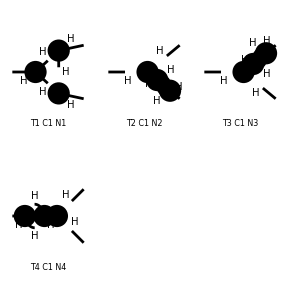

FeynArtsGraphics[{H}→{H,H}][([T1 C1 N1] | [T2 C1 N2] | [T3 C1 N3]
[T4 C1 N4] | Null | Null
Null | Null | Null)]

```mathematica
loop=CreateTopologies[1,1->2,ExcludeTopologies->Tadpoles];
insloop=InsertFields[loop,{S[1]}->{S[1],S[1]},Model->SM,InsertionLevel->{Classes},ExcludeParticles->{V,F,U,T,S[2],S[3]},ExcludeFieldPoints->{FieldPoint[0][S,S,S,S]}];
Paint[insloop]
```

```mathematica
SymmetryFactor[insloop[[1]][[1]]]
insloop[[1]][[1]]
```

1

Topology[1][Propagator[Incoming][Vertex[1][1],Vertex[3][4],Field[1]],Propagator[Outgoing][Vertex[1][2],Vertex[3][5],Field[2]],Propagator[Outgoing][Vertex[1][3],Vertex[3][6],Field[3]],Propagator[Loop[1]][Vertex[3][4],Vertex[3][5],Field[4]],Propagator[Loop[1]][Vertex[3][4],Vertex[3][6],Field[5]],Propagator[Loop[1]][Vertex[3][5],Vertex[3][6],Field[6]]]

```mathematica
p={p1,p2,p3,p4,p5,p6}
k={k1,k2,k3,k4,k5,k6}
l={l1,l2,l3,l4,l5,l6}
```

{p1,p2,p3,p4,p5,p6}

{k1,k2,k3,k4,k5,k6}

{l1,l2,l3,l4,l5,l6}

```mathematica
amploop=CreateFeynAmp[insloop][[1]][[3]]//.{FeynAmpDenominator:>Times,PropagatorDenominator[x_,MH]:>prop[x,0],FourMomentum[Incoming,x_]->p[[x]],FourMomentum[Outgoing,x_]->k[[x]],FourMomentum[Internal,x_]->l[[x]]}(*/.{SW->1,MW->1,MH->1,EL->1}*)
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

-(27 ⅈ EL^3 MH^6 prop[l1,0] prop[-k1+l1,0] prop[-k1-k2+l1,0])/(128 MW^3 π^4 SW^3)

```mathematica
FullForm[amploop]
```

Times[Complex[0,Rational[-27,128]],Power[EL,3],Power[MH,6],Power[MW,-3],Power[Pi,-4],Power[SW,-3],prop[l1,0],prop[Plus[Times[-1,k1],l1],0],prop[Plus[Times[-1,k1],Times[-1,k2],l1],0]]

True

```mathematica
propQ[elem_]:=MatchQ[elem,prop[__]]
notpropQ[elem_]:=Not[MatchQ[elem,prop[__]]]
propQ[amploop[[2]]]
```

False

```mathematica
covariantintegrand[ampexpr_]:=Module[{amplist},
amplist=List@@ampexpr;
{Times@@Select[amplist,notpropQ],Times@@Select[amplist,propQ]}
]
```

```mathematica
covariantintegrand[amploop]
```

{-(27 ⅈ EL^3 MH^6)/(128 MW^3 π^4 SW^3),prop[l1,0] prop[-k1+l1,0] prop[-k1-k2+l1,0]}

```mathematica
moms=FullForm[CreateFeynAmp[insloop][[1]][[3]]//.{FeynAmpDenominator:>Times}//Variables//Cases[_PropagatorDenominator]]//.{PropagatorDenominator[x_,MH]:>x}//.{FourMomentum[Incoming,x_]->p[[x]],FourMomentum[Outgoing,x_]->k[[x]],FourMomentum[Internal,x_]->l[[x]]}
```

creating amplitudes at level(s) {Classes}

> Top. 1: 1 Classes amplitude

> Top. 2: 1 Classes amplitude

> Top. 3: 1 Classes amplitude

> Top. 4: 1 Classes amplitude

in total: 4 Classes amplitudes

Part::pkspec1: The expression x cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

List[l1,Plus[Times[-1,k1],l1],Plus[Times[-1,k1],Times[-1,k2],l1]]

```mathematica
moms[[1]]
```

{l1,-k1+l1,-k1-k2+l1}

```mathematica
mommat=Replace[Table[{elem//.{Plus:>List}},{elem,moms[[1]]}],{x_List}:>x,{0,-3}]
```

{{l1},{-k1,l1},{-k1,-k2,l1}}

```mathematica
sigmat={}
```

{}

```mathematica
loopProducer[matrix_,loops_,in_,out_]:=Module[{flatlist, loopvec,sigmat,sigmaext,invec,outvec},
sigmat={};
sigmaext={};

For[i=1,i<=Length[matrix],i++,
flatlist=matrix[[i]]//.{Plus:>List};
loopvec=Table[0,{i,1,loops}];
invec=Table[0,{i,1,in}];
outvec=Table[0,{i,1,out}];
For[n=1, n<=Length[flatlist],n++,
For[j=1,j<=loops, j++,
If[flatlist[[n]]==l[[j]], loopvec[[j]]=1];
If[flatlist[[n]]==-l[[j]], loopvec[[j]]=-1];
];
For[j=1,j<=in, j++,
If[flatlist[[n]]==p[[j]], invec[[j]]=1];
If[flatlist[[n]]==-p[[j]], invec[[j]]=-1];
];
For[j=1,j<=out, j++,
If[flatlist[[n]]==k[[j]], outvec[[j]]=1];
If[flatlist[[n]]==-k[[j]], outvec[[j]]=-1];
];
];
AppendTo[sigmat,loopvec];
AppendTo[sigmaext,Join[invec,outvec]];
];
{sigmat,sigmaext}
]
```

```mathematica
loopProducer[mommat,1,1,2]
```

{{{1},{1},{1}},{{0,0,0},{0,-1,0},{0,-1,-1}}}

```mathematica
Import["https://github.com/apelloni/cLTD/raw/main/cLTD.m"]
SetOptions[cLTD,"FORMpath"->"/usr/local/bin/form",WorkingDirectory->"./"]
```

:::::::::::::::::::::::: cLTD ::::::::::::::::::::::::

Authors: Z. Capatti, V. Hirschi, D. Kermanschah, A. Pelloni, B. Ruijl

A Mathematica front end for cLTD [arxiv:2009.05509].

{loopmom→{k0,k1,k2,k3},FORMpath→/usr/local/bin/form,tFORMpath→tform,WorkingDirectory→./,FORM_ID→None,FORMcores→1,OptimizationLVL→0,keep_FORM_script→False,EvalAll→False,NoNumerator→False,FORMsubs→False,stdLTD→False}

```mathematica
ltdtriangle=cLTD[covariantintegrand[amploop][[2]],loopmom->{l1},stdLTD->True]
```

{cLTDnorm[-2 ⅈ E1] den[-E0^2+E1^2+2 E1 k1[0]+k1[0]^2] den[E1^2-E2^2-2 E1 k2[0]+k2[0]^2]+cLTDnorm[-2 ⅈ E0] den[E0^2-E1^2-2 E0 k1[0]+k1[0]^2] den[E0^2-E2^2-2 E0 k1[0]+k1[0]^2-2 E0 k2[0]+2 k1[0] k2[0]+k2[0]^2]+cLTDnorm[-2 ⅈ E2] den[-E1^2+E2^2+2 E2 k2[0]+k2[0]^2] den[-E0^2+E2^2+2 E2 k1[0]+k1[0]^2+2 E2 k2[0]+2 k1[0] k2[0]+k2[0]^2],{E0→√(l1.l1),E1→√(k1.k1-2 k1.l1+l1.l1),E2→√(k1.k1+2 k1.k2-2 k1.l1+k2.k2-2 k2.l1+l1.l1)}}

```mathematica
sptr=Table[{spanningTree/. {den[___]:>1,cLTDnorm[x__]:>Table[ToExpression[StringTake[ToString[Ei],-StringLength[ToString[Ei]]+1]],{Ei,Select[List@@x,Not[NumberQ[#]]&]}]},spanningTree},{spanningTree,List@@ltdtriangle[[1]]}]
```

{{{1},cLTDnorm[-2 ⅈ E1] den[-E0^2+E1^2+2 E1 k1[0]+k1[0]^2] den[E1^2-E2^2-2 E1 k2[0]+k2[0]^2]},{{0},cLTDnorm[-2 ⅈ E0] den[E0^2-E1^2-2 E0 k1[0]+k1[0]^2] den[E0^2-E2^2-2 E0 k1[0]+k1[0]^2-2 E0 k2[0]+2 k1[0] k2[0]+k2[0]^2]},{{2},cLTDnorm[-2 ⅈ E2] den[-E1^2+E2^2+2 E2 k2[0]+k2[0]^2] den[-E0^2+E2^2+2 E2 k1[0]+k1[0]^2+2 E2 k2[0]+2 k1[0] k2[0]+k2[0]^2]}}

```mathematica
q=S k + E p
k=IS q - IS E p
```

```mathematica
substitutionRules[mommat_,loops_,in_,out_]:=Module[{subrules,sigmatransf,indices,currentmatrix,inversesignaturematrix,externalmatrix,subrule},
subrules={};
sigmatransf=loopProducer[mommat,loops,in,out];
For[i==1, i<=Length[sptr],i++,
indices=sptr[[i]][[1]];
currentmatrix=sigmatransf[[indices]];
inversesignaturematrix=Inverse[Table[currentmatrix[[i]][[1]],{i,1,Length[currentmatrix]}]];
externalmatrix=inversesignaturematrix.Table[currentmatrix[[i]][[2]],{i,1,Length[currentmatrix]}];
subrule=Table[l[[i]]->Sum[inversesignaturematrix[[i,j]]lp[[j]] ,{j,1,loops}]-Sum[externalmatrix[[i,j]]pp[[j]] ,{j,1,in}]-Sum[externalmatrix[[i,j+in]]kp[[j]] ,{j,1,out}],{i,1,loops}];
AppendTo[subrules, subrule];
];
subrules
]
```

```mathematica
ltdtriangle[[2]]/.{k1->moms[2]}
```

{E0→√(MH^2+l1.l1),E1→√(MH^2+l1.l1-2 List[l1,Plus[Times[-1,k1],l1],Plus[Times[-1,k1],Times[-1,k2],l1]][2].l1+List[l1,Plus[Times[-1,k1],l1],Plus[Times[-1,k1],Times[-1,k2],l1]][2].List[l1,Plus[Times[-1,k1],l1],Plus[Times[-1,k1],Times[-1,k2],l1]][2]),E2→√(MH^2+k2.k2-2 k2.l1+l1.l1+2 List[l1,Plus[Times[-1,k1],l1],Plus[Times[-1,k1],Times[-1,k2],l1]][2].k2-2 List[l1,Plus[Times[-1,k1],l1],Plus[Times[-1,k1],Times[-1,k2],l1]][2].l1+List[l1,Plus[Times[-1,k1],l1],Plus[Times[-1,k1],Times[-1,k2],l1]][2].List[l1,Plus[Times[-1,k1],l1],Plus[Times[-1,k1],Times[-1,k2],l1]][2])}